## Parámetros

```mathematica
(*HNL DECAYS TOO MESONS/LEPTONS*)(*ESTE SCRIPT GENERA LOS ARCHIVOS PCONFIG QUE UTILIZA PYTHIA8.*)(*NOTAR QUE SIEMPRE TOMA COMO ARGUMENTO LA MASA DEL HNL*)e=0.5109989461*10^-3;
mu=105.6583745*10^-3;
tau=1.77686;
leptons={e,mu,tau};
tfactor=1.5193*10^24(*Para pasar de s a GeV^-1*);mmc=3*10^11(*para pasar de s a mm/c*);ckm=({{0.9742,0.2243,0.0365},{0.218,0.997,0.0422},{0.0081,0.0394,1.019}});
gf=1.166378*10^-5;
xw=0.2223;
gll=-(1/2)+xw;
glr=xw;

(*charged pseudoscalar*)
d431={504*10^-15*tfactor,1.96834,249.0*10^-3,ckm[[2,2]],431};
d431bar={504*10^-15*tfactor,1.96834,249.0*10^-3,ckm[[2,2]],-431};
d411={1040*10^-15*tfactor,1.86958,211.9*10^-3,ckm[[2,1]],411};
d411bar={1040*10^-15*tfactor,1.86958,211.9*10^-3,ckm[[2,1]],-411};
k321={1.238*10^-8*tfactor,493.677*10^-3,155.6*10^-3,ckm[[1,2]]};
pi211={2.6*10^-8*tfactor,139.57061*10^-3,130.2*10^-3,ckm[[1,1]]};

(*Charged vector*)
k323={Null,895.55*10^-3,0.1827,ckm[[1,2]]}(*K*(892)*);
rho770c={Null,775.26*10^-3,0.162,ckm[[1,1]]};

(*neutral pseudoscalar*)
pi111={Null,134.977*10^-3,130.2*10^-3,Null};
eta221={Null,547.862*10^-3,81.7*10^-3,Null}(*eta*);eta331={Null,957.78*10^-3,-94.7*10^-3,Null}(*eta prime*);(*Neutral vector*)
rho770n={Null,775.26*10^-3,0.162,1-2xw};
omega782={Null,782.65*10^-3,0.153,4/3 xw};
phi1020={Null,1.019461,0.234,4/3 xw-1};
```

## Funciones de Widths

```mathematica
lambda[a_,b_,c_]:=a^2+b^2+c^2-2a*b-2b*c-2c*a;
i1[x_,y_]:=Sqrt[lambda[1,x,y]]((1-x)^2-y(1+x));
i2[x_,y_]:=Sqrt[lambda[1,x,y]]((1+x-y)(1+x+2y)-4x);

i11[x_,y_,z_]:=12NIntegrate[1/s (s-x-y)(1+z-s)Sqrt[lambda[s,x,y]] Sqrt[lambda[1,s,z]],{s,(Sqrt[x]+Sqrt[y])^2,(1-Sqrt[z])^2},WorkingPrecision->MachinePrecision,AccuracyGoal->Automatic,MaxRecursion->Infinity,Method->"GlobalAdaptive" ];
i22[x_,y_,z_]:=24Sqrt[y*z]NIntegrate[1/s (1+x-s)Sqrt[lambda[s,y,z]] Sqrt[lambda[1,s,x]],{s,(Sqrt[y]+Sqrt[z])^2,(1-Sqrt[x])^2},WorkingPrecision->MachinePrecision,AccuracyGoal->Automatic,MaxRecursion->Infinity,Method->"GlobalAdaptive"];

datae=Import[NotebookDirectory[]<>"/mainconfig/mixe.dat"];
datamu=Join[Table[{i,1},{i,0.01,0.1,0.01}],Import[NotebookDirectory[]<>"/mainconfig/mixmu.dat"]];
datatau=Import[NotebookDirectory[]<>"/mainconfig/mixtau.dat"];
fmixe=Interpolation[datae,InterpolationOrder->1];
fmixmu=Interpolation[datamu,InterpolationOrder->1];
fmixtau=Interpolation[datatau,InterpolationOrder->1];

width01[n_,l_,h_,u_]:=h[[4]]^2 u^2 (gf^2 h[[3]]^2 n^3)/(16Pi) i1[(l/n)^2,(h[[2]]/n)^2](*P+*);
width02[n_,h_,u_]:=u^2*(gf^2 h[[3]]^2 n^3)/(16*Pi) i1[0,(h[[2]]/n)^2](*P0 ORIGINAL*);
width02[n_,h_,u_]:=u^2*(gf^2 h[[3]]^2 n^3)/(16*Pi) i1[0,(h[[2]]/n)^2](*P0 DEBUG*);
width03[n_,l_,h_,u_]:=(u^2*h[[4]]^2 gf^2 h[[3]]^2 n^3)/(16Pi*h[[2]]^2) i2[(l/n)^2,(h[[2]]/n)^2] (*V+*);
width04[n_,h_,u_]:=u^2*(gf^2 h[[3]]^2 h[[4]]^2 n^3)/(16Pi*h[[2]]^2) i2[0,(h[[2]]/n)^2](*V0*);
width05[n_,l1_,l2_,u_]:=(gf^2 n^5)/(192Pi^3) u^2 i11[0,(l1/n)^2,(l2/n)^2];
width06a[n_,l_,u_]:=(gf^2 n^5)/(96Pi^3) u^2 ((gll*glr+glr)i22[0,(l/n)^2,(l/n)^2]+(gll^2+glr^2+1+2gll)i11[0,(l/n)^2,(l/n)^2]);
width06b[n_,l_,u_]:=(gf^2 n^5)/(96Pi^3) u^2 ((gll*glr+0)i22[0,(l/n)^2,(l/n)^2]+(gll^2+glr^2+0)i11[0,(l/n)^2,(l/n)^2]);
(*nu_i nu_j nubar_j Notar que se ha dividido entre 3 para tomar cada término de la sumatoria de Pascoli2009 Eq.C.8*)
width07[n_,u_]:=u^2 (gf^2 n^5)/(3*96Pi^3)(* Modified pascoli *); 
width07[n_,u_]:=u^2 (gf^2 n^5)/(32Pi^3)(* Pascoli original, es el total nununu *); 
width07[n_,u_]:=u^2 (gf^2 n^5)/(768*Pi^3)(* Bondarenko *); 
width07[n_,u_]:=u^2 (gf^2 n^5)/(96*Pi^3)(* DEBUG *);
```

## Por sabor y TotalW

```mathematica
(*(1):N>l-P+*)
ePi[n_,u_]:=Re[width01[n,e,pi211,u]*UnitStep[n-pi211[[2]]-e]];
eK[n_,u_]:=Re[width01[n,e,k321,u]*UnitStep[n-k321[[2]]-e]];
eD[n_,u_]:=Re[width01[n,e,d411,u]*UnitStep[n-d411[[2]]-e]];
muPi[n_,u_]:=Re[width01[n,mu,pi211,u]*UnitStep[n-pi211[[2]]-mu]];
muK[n_,u_]:=Re[width01[n,mu,k321,u]*UnitStep[n-k321[[2]]-mu]];
muD[n_,u_]:=Re[width01[n,mu,d411,u]*UnitStep[n-d411[[2]]-mu]];
tauPi[n_,u_]:=Re[width01[n,tau,pi211,u]*UnitStep[n-pi211[[2]]-tau]];
tauK[n_,u_]:=Re[width01[n,tau,k321,u]*UnitStep[n-k321[[2]]-tau]];
tauD[n_,u_]:=Re[width01[n,tau,d411,u]*UnitStep[n-d411[[2]]-tau]];

(*(2):N>l-V+*)
eKstar[n_,u_]:=Re[width03[n,e,k323,u]*UnitStep[n-k323[[2]]-e]];
erhoc[n_,u_]:=Re[width03[n,e,rho770c,u]*UnitStep[n-rho770c[[2]]-e]];
muKstar[n_,u_]:=Re[width03[n,mu,k323,u]*UnitStep[n-k323[[2]]-mu]];
murhoc[n_,u_]:=Re[width03[n,mu,rho770c,u]*UnitStep[n-rho770c[[2]]-mu]];
tauKstar[n_,u_]:=Re[width03[n,tau,k323,u]*UnitStep[n-k323[[2]]-tau]];
taurhoc[n_,u_]:=Re[width03[n,tau,rho770c,u]*UnitStep[n-rho770c[[2]]-tau]];

(*(3):N>nu P0*)
nupi0[n_,u_]:=Re[width02[n,pi111,u]*UnitStep[n-pi111[[2]]]];
nueta[n_,u_]:=Re[width02[n,eta221,u]*UnitStep[n-eta221[[2]]]];
nuetaprime[n_,u_]:=Re[width02[n,eta331,u]*UnitStep[n-eta331[[2]]]];

(*(4):N>nu V0*)
nurho[n_,u_]:=Re[width04[n,rho770n,u]*UnitStep[n-rho770n[[2]]]];
nuomega[n_,u_]:=Re[width04[n,omega782,u]*UnitStep[n-omega782[[2]]]];
nuphi[n_,u_]:=Re[width04[n,phi1020,u]*UnitStep[n-phi1020[[2]]]];

(*(5) (par de leptones diferentes) N>l1-W+(W+ >l2+nu2)/l1≠l2*)
enumumu[n_,u_]:=Re[width05[n,e,mu,u]*UnitStep[n-e-mu]];
munuee[n_,u_]:=Re[width05[n,mu,e,u]*UnitStep[n-mu-e]];
enutautau[n_,u_]:=Re[width05[n,e,tau,u]*UnitStep[n-e-tau]];
taunuee[n_,u_]:=Re[width05[n,tau,e,u]*UnitStep[n-tau-e]];
munutautau[n_,u_]:=Re[width05[n,mu,tau,u]*UnitStep[n-mu-tau]];
taunumumu[n_,u_]:=Re[width05[n,tau,mu,u]*UnitStep[n-tau-mu]];

(*(6a) (par de leptones y neutrino iguales) N>nu1 l1-l1+*)
nueee[n_,u_]:=Re[width06a[n,e,u]*UnitStep[n-2e]];
numumumu[n_,u_]:=Re[width06a[n,mu,u]*UnitStep[n-2mu]];
nutautautau[n_,u_]:=Re[width06a[n,tau,u]*UnitStep[n-2tau]];

(*(6b) (par de leptones iguales,neutrino diferente) N>nu1 l2-l2+*)
nuemumu[n_,u_]:=Re[width06b[n,mu,u]*UnitStep[n-2mu]];
nuetautau[n_,u_]:=Re[width06b[n,tau,u]*UnitStep[n-2tau]];
numuee[n_,u_]:=Re[width06b[n,e,u]*UnitStep[n-2e]];
numutautau[n_,u_]:=Re[width06b[n,tau,u]*UnitStep[n-2tau]];
nutauee[n_,u_]:=Re[width06b[n,e,u]*UnitStep[n-2e]];
nutaumumu[n_,u_]:=Re[width06b[n,mu,u]*UnitStep[n-2mu]];

(*(7):nui nuj nujbar*)
nununu[n_,u_]:=Re[width07[n,u]];

(* Para Majorana todo se multiplican por dos, lo cual no cambia los BRs, pero sí el totalw y lifetime.*)
(* (1), (2) y (5) son especiales porque produce mesones con carga opuesta al caso Dirac. *)
(* En Majorana, en todos los casos se añaden BRs para el proceso y el procesos conjugado de carga *)
(*65 canales*)
totalw[n_,mixe_,mixmu_,mixtau_]:=
2*(ePi[n,mixe]+muPi[n,mixmu]+tauPi[n,mixtau]+eK[n,mixe]+muK[n,mixmu]+eD[n,mixe])(*1*)+
2*(eKstar[n,mixe]+muKstar[n,mixmu]+erhoc[n,mixe]+murhoc[n,mixmu])(*2*)+
1*(nupi0[n,mixe]+nupi0[n,mixmu]+nupi0[n,mixtau]+nueta[n,mixe]+nueta[n,mixmu]+nueta[n,mixtau]+nuetaprime[n,mixe]+nuetaprime[n,mixmu]+nuetaprime[n,mixtau])(*3*)+
1*(nurho[n,mixe]+nurho[n,mixmu]+nurho[n,mixtau]+nuomega[n,mixe]+nuomega[n,mixmu]+nuomega[n,mixtau]+nuphi[n,mixe]+nuphi[n,mixmu]+nuphi[n,mixtau])(*4*)+
2*(enumumu[n,mixe]+enutautau[n,mixe]+munuee[n,mixmu]+munutautau[n,mixmu]+taunuee[n,mixtau]+taunumumu[n,mixtau])(*5*)+
1*(nueee[n,mixe]+numumumu[n,mixmu])(*6a*)+
1*(numuee[n,mixmu]+nutauee[n,mixtau]+nuemumu[n,mixe]+nutaumumu[n,mixtau])(*6b*)+
3*(nununu[n,mixe])(*7*);
```

## All Plots

### Plots CC

```mathematica
tablecanalesCC[n_]:={ePi[n,1],muPi[n,1],eK[n,1],muK[n,1],erhoc[n,1],murhoc[n,1],eKstar[n,1],muKstar[n,1],eD[n,1],(enumumu[n,1]+munuee[n,1]),(enutautau[n,1]+taunuee[n,1]),tauPi[n,1],(munutautau[n,1]+taunumumu[n,1])};
plottheme = "Scientific";
scalingfunctions = {"Linear", "Log"};
plotrange = {{0, 2}, {10^-5, 1}};
imagesize={400,Automatic};
colours={Darker[Green,0.4],Darker[Green,0.4],Red,Red,Lighter[Orange,0.2],Lighter[Orange,0.2],Lighter[Blue,0.4],Lighter[Blue,0.4],Darker[Cyan,0.2],Purple,Yellow,Black,Pink};
styles={Automatic,Dashed,Automatic,Dashed,Automatic,Dashed,Automatic,Dashed,Automatic,Automatic,Automatic,Automatic,Automatic};
legends={"ePi","muPi","eK","muK","erhoc","murhoc","eKstar","muKstar","eD","nuemu","nuetau","taupi","numutau"};
```

```mathematica
plotsCC={};
Do[
plotCCaux=Plot[{(tablecanalesCC[n][[i]])/totalw[n,1,1,1]},{n,0.5,0.6},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->200,PlotStyle->{colours[[i]],styles[[i]]}];
AppendTo[plotsCC,plotCCaux];
,{i,1,13}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

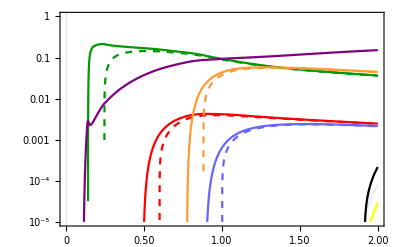

```mathematica
bg = Plot[Null, {x, 0.01, 2}, PlotTheme -> plottheme, ScalingFunctions -> scalingfunctions, PlotRange -> plotrange,ImageSize->imagesize,PlotPoints->200];
Show[bg,plotsCC]
```

### Plots NC

```mathematica
tablecanalesNC[n_]:={(4*nununu[n,1]+4*nununu[n,1]+4*nununu[n,1]),
(nueee[n,1]+numuee[n,1]+nutauee[n,1]),
(numumumu[n,1]+nuemumu[n,1]+nutaumumu[n,1]),
3*nupi0[n,1],3*nurho[n,1],3*nuomega[n,1],3*nueta[n,1],3*nuetaprime[n,1],3*nuphi[n,1]};
```

```mathematica
plottheme = "Scientific";
scalingfunctions = {"Linear", "Log"};
plotrange = {{0, 2}, {10^-5, 1}};
imagesize={400,Automatic};
```

```mathematica
colours={Purple,Darker[Green,0.4],Darker[Green,0.4],Darker[Cyan,0.2],Lighter[Orange,0.2],Lighter[Blue,0.3],Red,Red,Black};
styles={Automatic,Automatic,Dashed,Automatic,Automatic,Automatic,Automatic,Dashed,Automatic};
legends={"nununu","nuee","numumu","nupi0","nurho0","nuomega","nueta","nuetaprime","nuphi"};
```

```mathematica
plotsNC={};
Do[
plotNCaux=Plot[{(tablecanalesNC[n][[i]])/totalw[n,1,1,1]},{n,0.01,2},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->200,PlotStyle->{colours[[i]],styles[[i]]}];
AppendTo[plotsNC,plotNCaux];
,{i,1,Length@legends}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

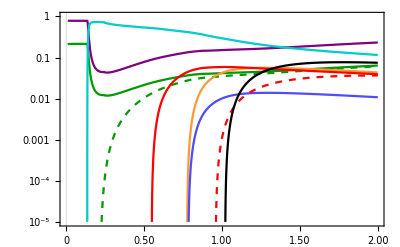

```mathematica
bg = Plot[Null, {x, 0.01, 2}, PlotTheme -> plottheme, ScalingFunctions -> scalingfunctions, PlotRange -> plotrange,ImageSize->imagesize,PlotPoints->200];
Show[bg,plotsNC]
```

## Plots Debug

### Canales y Config

```mathematica
tablecanalesCC[n_]:={2*ePi[n,1],2*muPi[n,1],2*(enumumu[n,1]+munuee[n,1])};
tablecanalesNC[n_]:={(4*nununu[n,1]+4*nununu[n,1]+4*nununu[n,1]),(nueee[n,1]+numuee[n,1]+nutauee[n,1]),3*nupi0[n,1]};
plottheme = "Scientific";
scalingfunctions = {"Linear", "Log"};
plotrange = {{0, 2}, {10^-5, 1}};
imagesize={400,Automatic};
coloursCC={Darker[Green,0.4],Darker[Green,0.4],Purple};
stylesCC={Automatic,Dashed,Automatic};
legendsCC={"ePi","muPi","nuemu"};
coloursNC={Purple,Darker[Green,0.4],Cyan};
stylesNC={Automatic,Automatic,Automatic};
legendsNC={"nununu","nuee","nupi0"};
bg = Plot[Null, {x, 0.01, 2}, PlotTheme -> plottheme, ScalingFunctions -> scalingfunctions, PlotRange -> plotrange,ImageSize->imagesize,PlotPoints->200];
```

### CC

```mathematica
plotsCC={};
Do[
plotaux=Plot[{(tablecanalesCC[n][[i]])/totalw[n,1,1,1]},{n,0.01,2},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->200,PlotStyle->{coloursCC[[i]],stylesCC[[i]]}];
AppendTo[plotsCC,plotaux];
,{i,1,Length@coloursCC}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

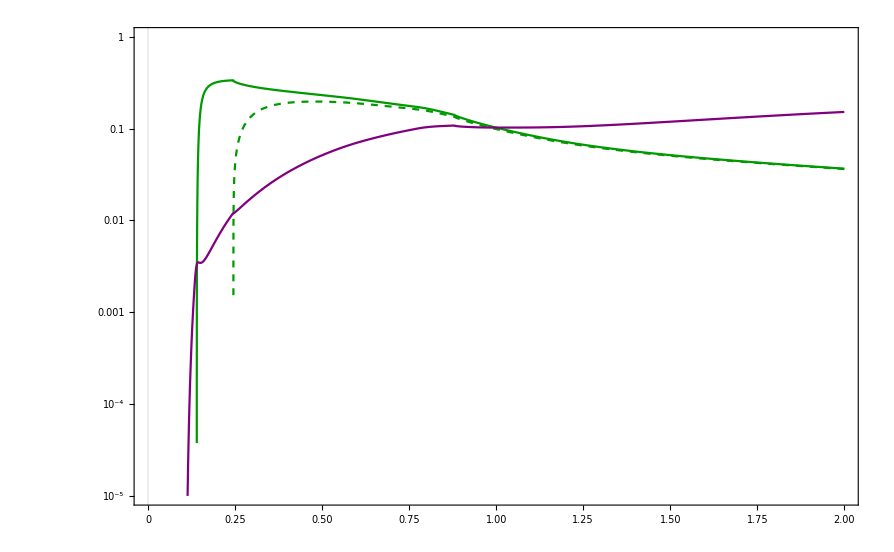

```mathematica
Show[bg,plotsCC]
```

### NC

```mathematica
plotsNC={};
Do[
plotaux=Plot[{(tablecanalesNC[n][[i]])/totalw[n,1,1,1]},{n,0.01,2},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->200,PlotStyle->{coloursNC[[i]],stylesNC[[i]]}];
AppendTo[plotsNC,plotaux];
,{i,1,Length@coloursNC}]
```

### ShowPlots

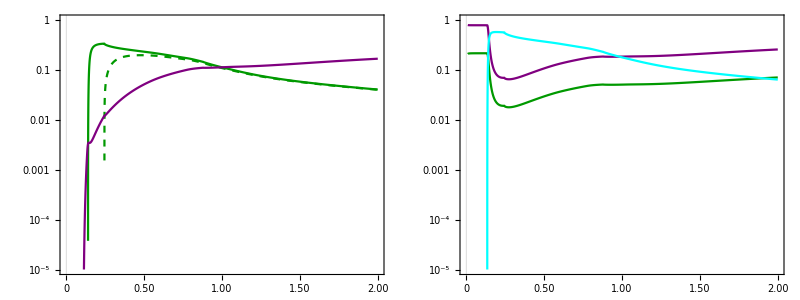

```mathematica
Grid[{{Show[bg,plotsCC],Show[bg,plotsNC]}}]
```

```mathematica
Grid
```

## Meson BRs

```mathematica
(***************MESON DECAY*******************)
(*meson decay BRs function*)
width2body[meson_,l_,n_,u_]:=Re[(gf^2*meson[[3]]^2*meson[[2]]*n^2)/(8*Pi)*meson[[4]]^2*u^2*(1-n^2/meson[[2]]^2+2l^2/meson[[2]]^2+l^2/n^2(1-l^2/meson[[2]]^2))*Sqrt[(1+n^2/meson[[2]]^2-l^2/meson[[2]]^2)^2-4*n^2/meson[[2]]^2]*UnitStep[meson[[2]]-l]];
newwidth[meson_,n_,mixe_,mixmu_,mixtau_]:=Re[1/meson[[1]]+width2body[meson,e,n,mixe]+width2body[meson,mu,n,mixmu]+width2body[meson,tau,n,mixtau]];
newwidth2hnl[meson_,n_,mixe_,mixmu_,mixtau_]:=Re[width2body[meson,e,n,mixe]+width2body[meson,mu,n,mixmu]+width2body[meson,tau,n,mixtau]];
(*BRs solo a HNL,normalizados a 1*)
meson2bodybr[meson_,l_,n_,u_,mixe_,mixmu_,mixtau_]:=Re[width2body[meson,l,n,u]/newwidth2hnl[meson,n,mixe,mixmu,mixtau]];

(*HNL LIFETIME*)
lifetime[n_,mixe_,mixmu_,mixtau_]:=Quiet[Re[1/totalw[n,mixe,mixmu,mixtau]]*1/tfactor*mmc];
```